# Interactive visualization of two-dimensional Euclidean space

## Définition du produit scalaire

```mathematica
⟨x_|y_⟩:=∑_(i=1)^Length[x] x⟦i⟧y⟦i⟧
```

## Norme et normalization

### Norme

```mathematica
norm[x_]:=√⟨x|x⟩
```

### Normalization

```mathematica
normalize[x_]:=x/(√⟨x|x⟩)
```

### Normalization d’un ensemble

```mathematica
normalizeListe[vectors_]:=Table[normalize[vectors[[i]]],{i,1,Length[vectors]}]
```

## Projection orthogonale

```mathematica
projection[y_,x_]:=⟨x|y⟩x/⟨x|x⟩
```

## Orthogonalisation (Procédé de Gram-Schmidt)

```mathematica
gramSchmidt[vectors_]:=Module[{oVectors=vectors},
Do[oVectors[[i]]-=projection[oVectors[[i]],oVectors[[j]]],{i,2,Length[vectors]},{j,1,i-1}];
oVectors]
```

### Matrice d’orthonormalité

```mathematica
orthogonality[vectors_]:=Table[⟨vectors[[i]]|vectors[[j]]⟩,{i,1,Length[vectors]},{j,1,Length[vectors]}]//Simplify//TableForm
```

## Show

```mathematica
showVectors[vectors_]:=Graphics[{Blue,Map[Arrow[{{0,0},#}]&,vectors]},ImageSize->Small]
```

```mathematica
Project[a_,vectors_]:=Map[projection[a,#]&,vectors]
```

```mathematica
showProjections[a_,vectors_]:=Graphics[{Dashed,Red,Map[Arrow[{{0,0},#}]&,Project[a,vectors]]}]
```

```mathematica
showAll[a_,vectors_]:=Show[{showVectors[vectors],Graphics[{Red,Arrow[{{0,0},a}]}],showProjections[a,vectors]}]
```

## La base

### Base quelconque

La dimension de la base

```mathematica
dim:=2
```

```mathematica
baseQuelconque={{4,5},{3,5}}
```

{{4,5},{3,5}}

```mathematica
orthogonality[baseQuelconque]
```

41 | 37
37 | 34

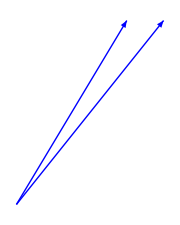

```mathematica
showVectors[baseQuelconque]
```

### Base orthogonale

```mathematica
baseOrthogonale=gramSchmidt[baseQuelconque]
```

{{4,5},{-25/41,20/41}}

```mathematica
orthogonality[baseOrthogonale]
```

41 | 0
0 | 25/41

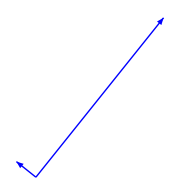

```mathematica
showVectors[baseOrthogonale]
```

### Base orthonormale

```mathematica
baseOrthonormale=normalizeListe[baseOrthogonale]//Simplify
```

{{4/(√41),5/(√41)},{-5/(√41),4/(√41)}}

```mathematica
orthogonality[baseOrthonormale]
```

1 | 0
0 | 1

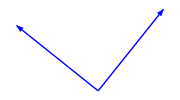

```mathematica
showVectors[baseOrthonormale]
```

## Développement du vecteur U sur une base

### Le vecteur à développer

```mathematica
U = {2,3};
```

### Sur la base quelconque

```mathematica
u:=baseQuelconque
```

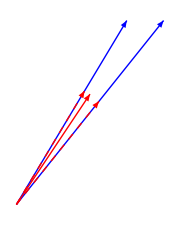

```mathematica
showAll[U,u]
```

Les coéfficients

```mathematica
Subscript[c, n_]:=⟨u[[n]]|U ⟩
```

```mathematica
Table[Subscript[c, n],{n,1,dim}]//Simplify
```

{23,21}

Développement

```mathematica
∑_(n=1)^dim Subscript[c, n] Subscript[𝓊, n]//Simplify
```

23 𝓊_1+21 𝓊_2

```mathematica
∑_(n=1)^dim Subscript[c, n] u[[n]]//Simplify
```

{155,220}

### Sur la base orthogonale

```mathematica
u:=baseOrthogonale
```

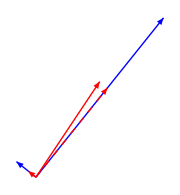

```mathematica
showAll[U,u]
```

Les coéfficients

```mathematica
Subscript[c, n_]:=⟨u[[n]]|U ⟩
```

```mathematica
Table[Subscript[c, n],{n,1,dim}]//Simplify
```

{23,10/41}

Développement

```mathematica
∑_(n=1)^dim Subscript[c, n] Subscript[𝓊, n]//Simplify
```

23 𝓊_1+(10 𝓊_2)/41

```mathematica
∑_(n=1)^dim Subscript[c, n] u[[n]]//Simplify
```

{154402/1681,193515/1681}

### Sur la base Orthonormale

```mathematica
u:=baseOrthonormale
```

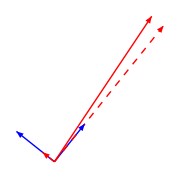

```mathematica
showAll[U,u]
```

Les coéfficients

```mathematica
Subscript[c, n_]:=⟨u[[n]]|U ⟩
```

```mathematica
Table[Subscript[c, n],{n,1,dim}]//Simplify
```

{23/(√41),2/(√41)}

Développement

```mathematica
∑_(n=1)^dim Subscript[c, n] Subscript[𝓊, n]//Simplify
```

(23 𝓊_1+2 𝓊_2)/(√41)

```mathematica
∑_(n=1)^dim Subscript[c, n] u[[n]]//Simplify
```

{2,3}